```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
<<Notation`
Symbolize[â]
Symbolize[E^*]
Symbolize[Subscript[u, z]]
Names["Global`*"]
```

{a⎵Overscript⎵Wedge,E⎵Superscript⎵Times,u⎵Subscript⎵z}

```mathematica
p[r_,ℓ_,P_]:=P/(π ℓ^2) ⅇ^(-(r/ℓ)^2)
χ[â:_,ℓ_,P_]=4/(SuperStar[E] π) Integrate[(p[r,ℓ,P]r)/(√(r^2-(â)^2)),{r,â,∞},Assumptions->0<â &&  0<ℓ]
Subscript[u, z][y_,ℓ_,P_]=Integrate[χ[x,ℓ,P]/(√(y^2-x^2)),{x,0,y},Assumptions->0<y  && 0<ℓ]
```

(2 ⅇ^(-(â)^2/ℓ^2) P)/(E^* π^(3/2) ℓ)

(ⅇ^(-y^2/(2 ℓ^2)) P BesselI[0,y^2/(2 ℓ^2)])/(E^* √π ℓ)

(A ⅇ^(-y^2/(2 ℓ^2)) √π ℓ BesselI[0,y^2/(2 ℓ^2)])/E^*

```mathematica
χ[r,ℓ,P]
Subscript[u, z][r,ℓ,P]
```

(2 ⅇ^(-r^2/ℓ^2) P)/(E^* π^(3/2) ℓ)

(ⅇ^(-r^2/(2 ℓ^2)) P BesselI[0,r^2/(2 ℓ^2)])/(E^* √π ℓ)

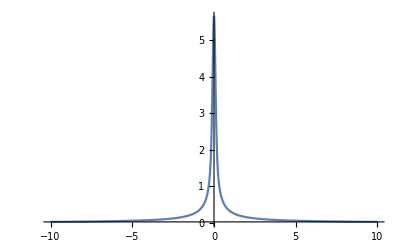

```mathematica
Plot[Subscript[u, z][r,0.1,1]/.SuperStar[E]->1,{r,-10,10},PlotRange->All]
```

```mathematica
Integrate[2π p[r,ℓ,A]r,{r,0,∞}]
```

ConditionalExpression[A π ℓ^2,Re[ℓ^2]>0]